```mathematica
(*1*)
ClearAll;
```

```mathematica
f[x_]=(x((x-4)^3+3 x))/(x+1)
```

(x ((-4+x)^3+3 x))/(1+x)

```mathematica
(*α*)
```

```mathematica
df[x_]=D[f[x],x]//FullSimplify
```

64-128/(1+x)^2+x (-26+3 x)

```mathematica
(*β*)
```

```mathematica
Intf[x_]=Integrate[f[x],x]//FullSimplify
```

1/12 (1+x) (-1975+x (439+x (-55+3 x)))+128 Log[1+x]

```mathematica
(*γ*)
```

```mathematica
N[Integrate[f[x],{x,0,1}]//FullSimplify]
```

-11.3605

```mathematica
(*δ*)
```

```mathematica
N[Solve[f[x]==0,x]//FullSimplify]
```

{{x→0.},{x→2.14111},{x→4.92944+2.36466 ⅈ},{x→4.92944-2.36466 ⅈ}}

```mathematica
(*ε*)
```

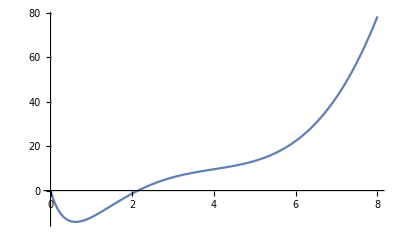

```mathematica
Plot[f[x],{x,0,8}]
```

```mathematica
(*στ*)
```

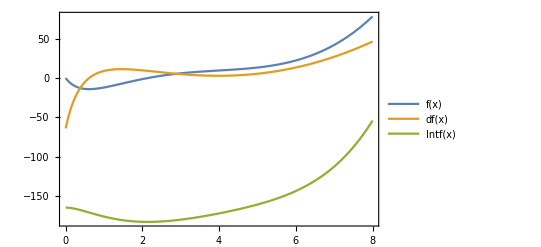

```mathematica
Plot[{f[x],df[x],Intf[x]},{x,0,8},Frame->True,PlotLegends->"Expressions"]
```

```mathematica
Int2f[y_]=Integrate[f[x],{x,0,y}]
```

ConditionalExpression[1/12 y (-1536+y (384+y (-52+3 y)))+128 Log[1+y],Re[y]>-1||y∉ℝ]

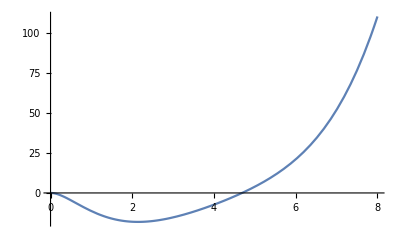

```mathematica
Plot[Int2f[x],{x,0,8}]
```

```mathematica
(*2*)
ClearAll;
```

```mathematica
f[x_]=x^2+8 (Sin[x^2] Exp[x])/(Exp[x]+1)
```

x^2+(8 ⅇ^x Sin[x^2])/(1+ⅇ^x)

```mathematica
(*α*)
```

```mathematica
df[x_]=D[f[x],x]
```

2 x+(16 ⅇ^x x Cos[x^2])/(1+ⅇ^x)-(8 ⅇ^(2 x) Sin[x^2])/((1+ⅇ^x)^2)+(8 ⅇ^x Sin[x^2])/(1+ⅇ^x)

```mathematica
(*β*)
```

```mathematica
Intf[x_]:=NIntegrate[f[k],{k,0,x}]
```

```mathematica
(*γ*)
```

```mathematica
N[Integrate[f[x],{x,0,1}]]
```

2.01073

```mathematica
(*δ*)
```

```mathematica
N[Reduce[f[x]==0&&0≤x≤3,x]]
```

x==0.||x==1.92362||x==2.33259

```mathematica
(*ε*)
```

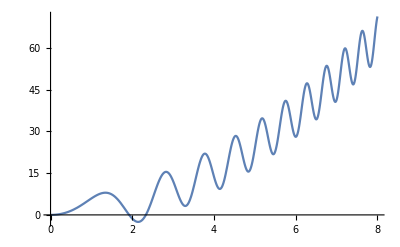

```mathematica
Plot[f[x],{x,0,8}]
```

```mathematica
(*στ*)
```

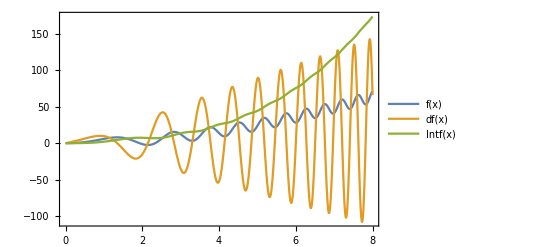

```mathematica
Plot[{f[x],df[x],Intf[x]},{x,0,8},Frame->True,PlotLegends->"Expressions"]
```

```mathematica
Int2f[y_]:=NIntegrate[f[x],{x,0,y}]
```

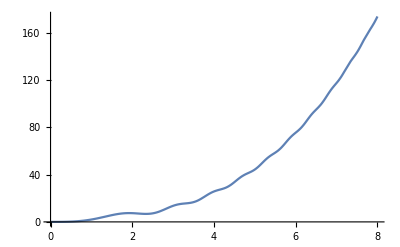

```mathematica
Plot[Int2f[x],{x,0,8}]
```